```mathematica
(* Mathematica Package *)
(* Created by Mathematica Plugin for IntelliJ IDEA *)

(* :Title: ExData *)
(* :Context: ExData` *)
(* :Author: GalAster *)
(* :Date: 2016-10-22 *)

(* :Package Version: 0.1 *)
(* :Update: 2016-10-22 *)
(* :Mathematica Version: 11.0+ *)
(* :Copyright:该软件包遵从CC协议:BY+NA+NC(署名、非商业性使用、相同方式共享） *)
(* :Keywords: *)
(* :Discussion: *)
```

```mathematica
BeginPackage["ExData`"]
Begin["`Private`"]
```

ExData`

ExData`Private`

```mathematica
DDD =TraditionalForm@{{边长a*正多面体[面], 表面积, 体积, 
     顶球半径, 棱球半径, 面球半径, 顶数, 棱数, 
     面数}, {正四面体[三角形], Sqrt[3]*a^2, 
     a^3/(6*Sqrt[2]), (1/2)*Sqrt[3/2]*a, a/(2*Sqrt[2]), 
     a/(2*Sqrt[6]), 4, 6, 4}, {正六面体[正方形], 6*a^2, 
     a^3, (Sqrt[3]*a)/2, a/Sqrt[2], a/2, 8, 12, 6}, 
    {正八面体[三角形], 2*Sqrt[3]*a^2, (Sqrt[2]*a^3)/3, 
     a/Sqrt[2], a/2, a/Sqrt[6], 6, 12, 8}, 
    {正十二面体[五边形], 3*Sqrt[25 + 10*Sqrt[5]]*a^2, 
     (1/4)*(15 + 7*Sqrt[5])*a^3, Sqrt[9/8 + 11/(8*Sqrt[5])]*a, 
     Sqrt[7/8 + 11/(8*Sqrt[5])]*a, Sqrt[5/8 + 11/(8*Sqrt[5])]*a, 
     20, 30, 12}, {正二十面体[三角形], 5*Sqrt[3]*a^2, 
     (1/12)*(15 + 5*Sqrt[5])*a^3, Sqrt[19/24 + Sqrt[5]/8]*a, 
     Sqrt[13/24 + Sqrt[5]/8]*a, ((3 + Sqrt[5])*a)/(4*Sqrt[3]), 
     12, 30, 20}}; 
bbb={-Graphics-,-Graphics-,-Graphics-,-Graphics-};
mb=-Graphics-;
```

```mathematica
End[] 

EndPackage[]
```

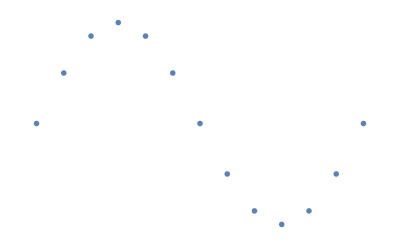

```mathematica
ListPlot[Table[{x,Sin[x]},{x,0,2 π,π/6}],Axes->None,PlotMarkers->mb,PlotRangePadding->.05]
```